```mathematica
(* setup constants *)
```

```mathematica
offset=Pi/7;
offset=0.196349540849362;
consts={ph->0+offset,al->60*Pi/180,r->1}
consts2={ph->Pi+offset,al->60*Pi/180,r->1}
```

{ph→0.19635,al→π/3,r→1}

{ph→3.33794,al→π/3,r→1}

```mathematica
(* setup tilted dipole *)
```

0

(Cos[ph] Sin[al])/r

(Sin[h] (Cos[al] Sin[h]-Cos[h] Sin[al] Sin[ph]))/r

(-0.168953 Cos[h]+Sin[h]/2) Sin[h]

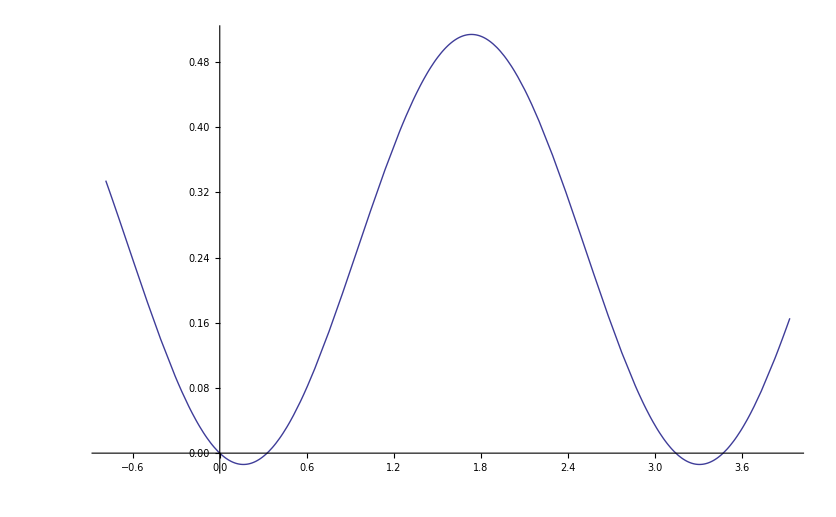

(Sin[al] Sin[ph])/r+(Cos[h] (Cos[al] Sin[h]-Cos[h] Sin[al] Sin[ph]))/r+(Sin[h] (Cos[al] Cos[h]+Sin[al] Sin[h] Sin[ph]))/r

Csc[h] ((Sin[al] Sin[ph])/r+(Cos[h] (Cos[al] Sin[h]-Cos[h] Sin[al] Sin[ph]))/r+(Sin[h] (Cos[al] Cos[h]+Sin[al] Sin[h] Sin[ph]))/r)

Csc[h] (0.168953+Cos[h] (-0.168953 Cos[h]+Sin[h]/2)+(Cos[h]/2+0.168953 Sin[h]) Sin[h])

0.168953+Cos[h] (-0.168953 Cos[h]+Sin[h]/2)+(Cos[h]/2+0.168953 Sin[h]) Sin[h]

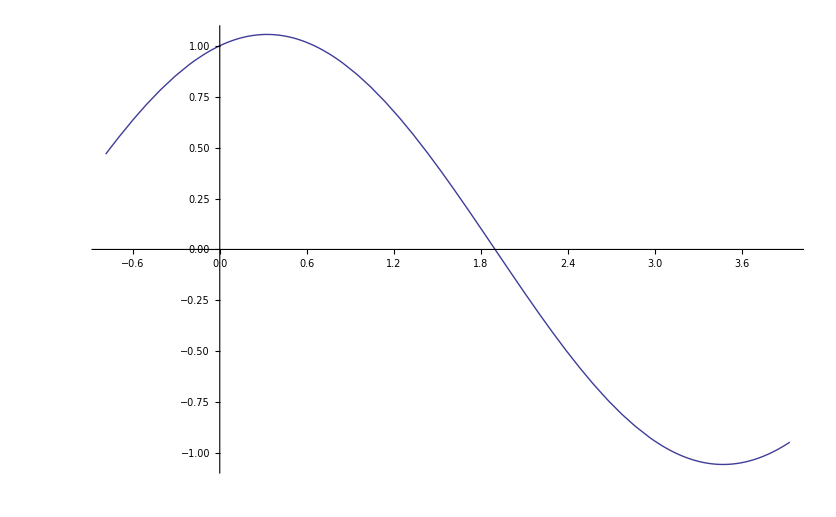

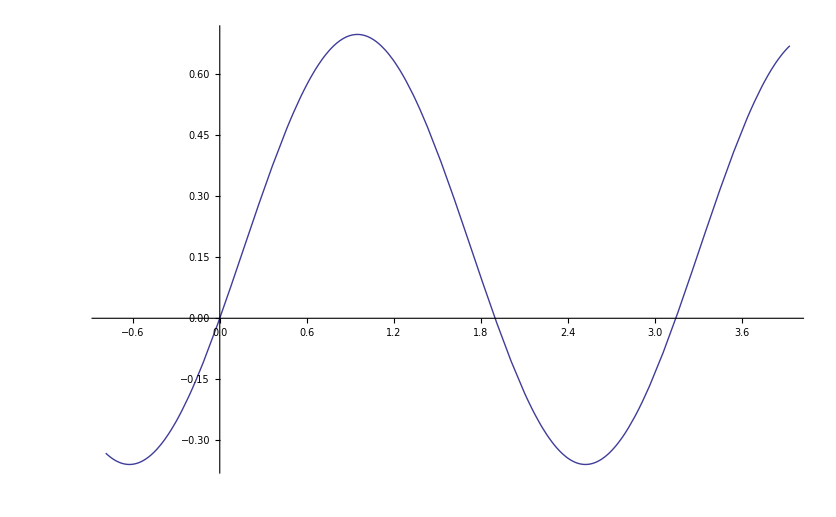

```mathematica
(*atheta=-Sin[al]*Sin[ph]*)
(*aphi=Sin[h]*(-Cos[h]*Cos[ph]*Sin[al]+Cos[al]*Sin[h])/r*)
ar=0
atheta=(1/r)*(Sin[al]*Cos[ph])
aphi=Sin[h]*(-Cos[h]*Sin[ph]*Sin[al]+Cos[al]*Sin[h])/r
aphinum=aphi//.consts
p1=Plot[aphinum,{h,-Pi/4,Pi+Pi/4}]
gdetB1=(D[aphi,h]-D[atheta,ph])
B1=gdetB1/Sin[h]
B1num=B1//.consts
gdetB1num=gdetB1//.consts
p1B=Plot[B1num,{h,-Pi/4,Pi+Pi/4}]
p1gB=Plot[gdetB1num,{h,-Pi/4,Pi+Pi/4}]
```

(Sin[h] (Cos[al] Sin[h]-Cos[h] Sin[al] Sin[ph]))/r^2

(Cos[al] Sin[h]-Cos[h] Sin[al] Sin[ph])/r^2

-0.168953 Cos[h]+Sin[h]/2

(-0.168953 Cos[h]+Sin[h]/2) Sin[h]

0.168953 Cos[h]+Sin[h]/2

(0.168953 Cos[h]+Sin[h]/2) Sin[h]

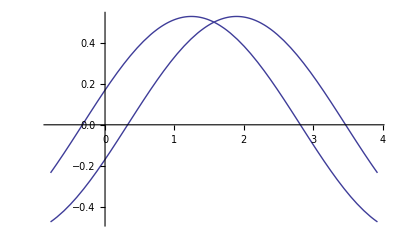

```mathematica
gdetB2=-(D[aphi,r]-D[ar,ph])
B2=gdetB2/Sin[h]
B2num=B2//.consts
gdetB2num=gdetB2//.consts
p2B=Plot[B2num,{h,-Pi/4,Pi+Pi/4}];
p2gB=Plot[gdetB2num,{h,-Pi/4,Pi+Pi/4}];
B2num2=B2//.consts2
gdetB2num2=gdetB2//.consts2
p2B2=Plot[B2num2,{h,-Pi/4,Pi+Pi/4}];
p2gB2=Plot[gdetB2num2,{h,-Pi/4,Pi+Pi/4}];
Show[{p2B,p2B2}]
```

0

0

0

«3 more identical outputs»

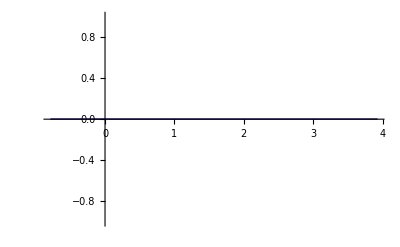

```mathematica
gdetB3=-(D[ar,h])
B3=gdetB3/Sin[h]
B3num=B3//.consts
gdetB3num=gdetB3//.consts
p3B=Plot[B3num,{h,-Pi/4,Pi+Pi/4}];
p3gB=Plot[gdetB3num,{h,-Pi/4,Pi+Pi/4}];
B3num2=B3//.consts2
gdetB3num2=gdetB3//.consts2
p3B2=Plot[B3num2,{h,-Pi/4,Pi+Pi/4}];
p3gB2=Plot[gdetB3num2,{h,-Pi/4,Pi+Pi/4}];
Show[{p3B,p3B2}]
```

```mathematica
(* get grid-based derivatives of A_i so can get B^r *)
```

16

8

-10

27

26

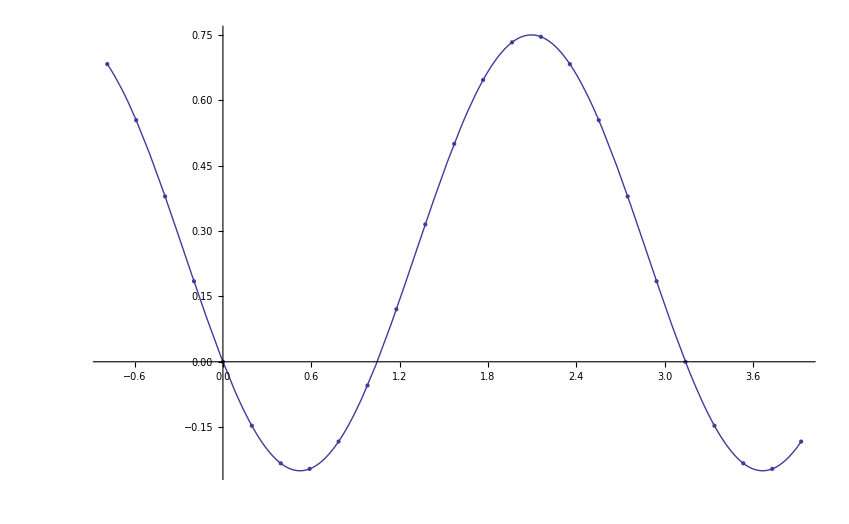

```mathematica
N2=16
N3=8
tjs=-10
tjfe=N2+11
tjfc=N2+10
hetab=Table[0+Pi*(tj-0)/(N2-0),{tj,tjs,tjfe}];
hctab=Table[0+Pi*(tj+0.5-0)/(N2-0),{tj,tjs,tjfc}];
aphitj=aphi//.{h->0+Pi*(tj-0)/(N2-0)};
aphitab=Table[aphitj,{tj,tjs,tjfe}];
phicvstk=0+2*Pi*(tk+0.5-0)/(N3-0);
tks=-10;
tkfc=N3+10;
phictab=Table[phicvstk,{tk,tks,tkfc}];
athetatk=atheta//.{ph->phicvstk};
athetatab=Table[athetatk,{tk,tks,tkfc}];
aphitabtoplot=Table[{hetab[[tj]],aphitab[[tj]]},{tj,1,1+tjfe-tjs}]//.consts;
p2=ListPlot[aphitabtoplot];
Show[{p1,p2}]
```

```mathematica
(* So A_\phi looks fine before taking derivative and dividing by sin(\theta) *)
```

```mathematica
(* detg B1 = A_\phi,\theta - A_\theta,\phi *)
```

```mathematica
thetk=1+Solve[phicvstk==ph//.consts,tk][[1,1,2]]-tks
tkup=IntegerPart[thetk]
tkdn=Ceiling[thetk]
```

10.5

10

11

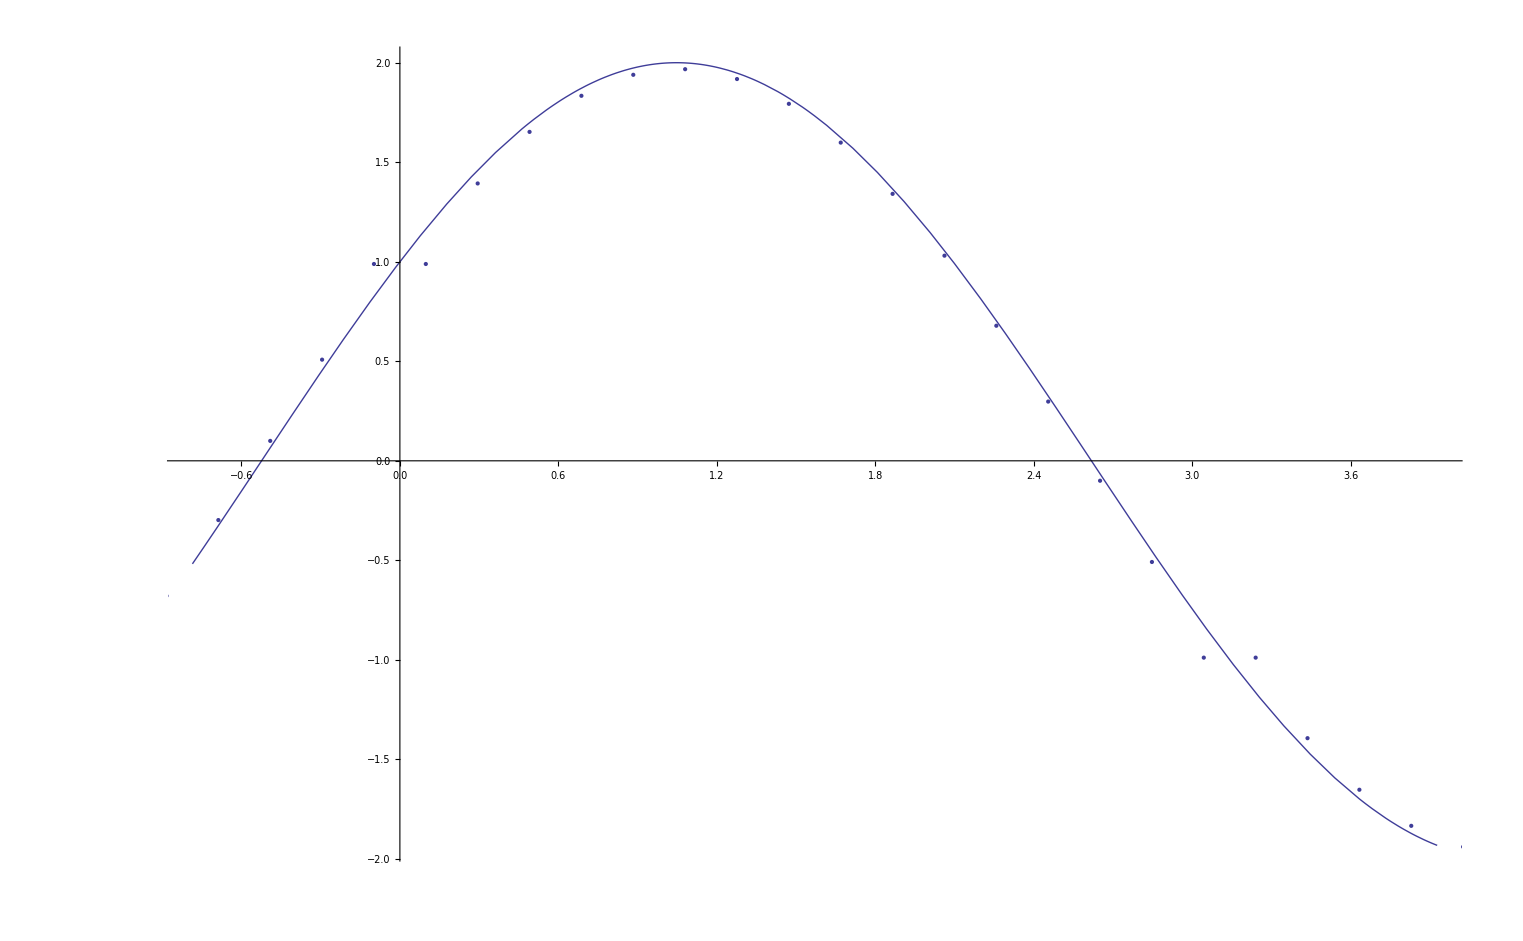

```mathematica
B1b=-(athetatab[[tkup]]-athetatab[[tkdn]])/(phictab[[tkup]]-phictab[[tkdn]]);
B1a=Table[(aphitab[[tj+1]]-aphitab[[tj]])/(hetab[[tj+1]]-hetab[[tj]]),{tj,1,1+tjfc-tjs}];
B1ab=Table[(B1a[[tj]]+B1b)/Sin[hctab[[tj]]],{tj,1,1+tjfc-tjs}];
B1abnum=B1ab//.consts;
B1toplot=Table[{hctab[[tj]],B1abnum[[tj]]},{tj,1,1+tjfc-tjs}]//.consts;
p2B=ListPlot[B1toplot];
Show[{p1B,p2B}]
```

```mathematica
(* So glitch present at the poles.  If I use N2=16 and N1=8, then points are flat across the axes just like in HARM.  Only using N1=N2=128 has no noticible issue.  Oddly, for N2=128 N3=32, gtlich has a varying sign of derivative across the pole -- like too much N2 resolution for the poor N3 resolution *)
```

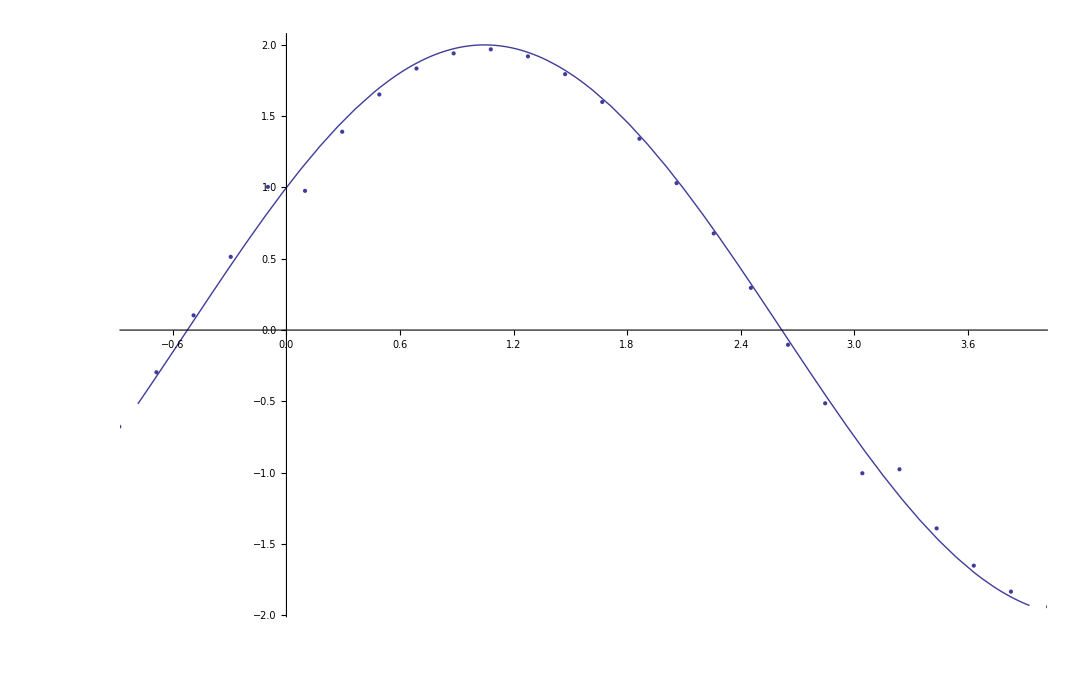

```mathematica
(* try volume reg -- this would ruin divB=0 as normally defined, but just check *)
modB1a=Table[-(aphitab[[tj+1]]-aphitab[[tj]])/(Cos[hetab[[tj+1]]]-Cos[hetab[[tj]]]),{tj,1,1+tjfc-tjs}];
B1ab=Table[modB1a[[tj]]+B1b/Sin[hctab[[tj]]],{tj,1,1+tjfc-tjs}];
B1abnum=B1ab//.consts;
B1toplot=Table[{hctab[[tj]],B1abnum[[tj]]},{tj,1,1+tjfc-tjs}]//.consts;
p2B=ListPlot[B1toplot];
Show[{p1B,p2B}]
```

```mathematica
(* No help for any resolution choices -- or makes a bit worse for N2=16 and N3=8 -- gves derivative change in sign across pole *)
```

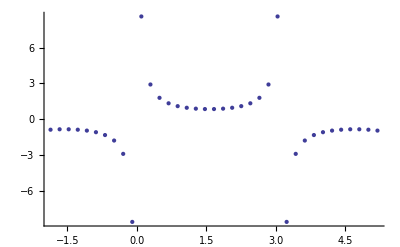

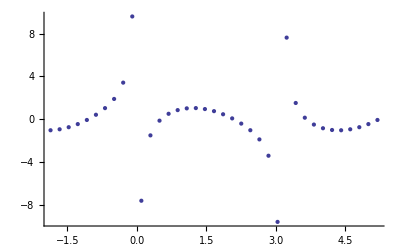

```mathematica
(* So, issue is cancellation between cross terms *)
B1btab=Table[B1b/Sin[hctab[[tj]]],{tj,1,1+tjfc-tjs}]//.consts;
B1btabtoplot=Table[{hctab[[tj]],B1btab[[tj]]},{tj,1,1+tjfc-tjs}]//.consts;
B1atabtoplot=Table[{hctab[[tj]],modB1a[[tj]]},{tj,1,1+tjfc-tjs}]//.consts;
ListPlot[B1btabtoplot]
ListPlot[B1atabtoplot]
```

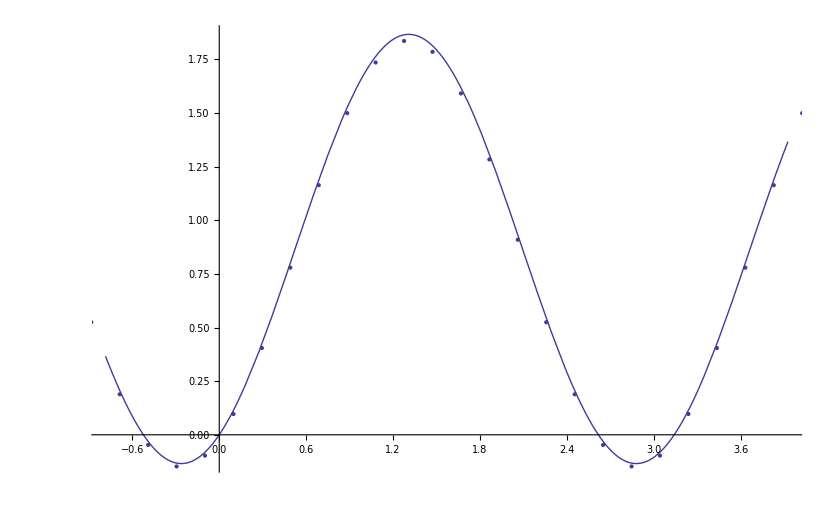

```mathematica
(* note that \detg B1 looks fine *)
B1b=-(athetatab[[tkup]]-athetatab[[tkdn]])/(phictab[[tkup]]-phictab[[tkdn]]);
B1a=Table[(aphitab[[tj+1]]-aphitab[[tj]])/(hetab[[tj+1]]-hetab[[tj]]),{tj,1,1+tjfc-tjs}];
B1ab=Table[(B1a[[tj]]+B1b),{tj,1,1+tjfc-tjs}];
B1abnum=B1ab//.consts;
B1toplot=Table[{hctab[[tj]],B1abnum[[tj]]},{tj,1,1+tjfc-tjs}]//.consts;
p2B=ListPlot[B1toplot];
Show[{p1gB,p2B}]
```

```mathematica
(* So perhaps we should interpolate \detg B1 and \detg B3 for the interpolation in the 2-direction.  This will avoid the interpolation seeing the glitch *)
(* This is fine since these quantities are not right on the pole until one interpolates to the pole for them, and them ending up on the pole works for the full3d method since with \detg the functions will smoothly pass thorugh the axis.*)
(*  Right now in HARM, the polar values of B1,B3 will be very off from the dipole, so the interpolation is probably completely reducing there *)
```

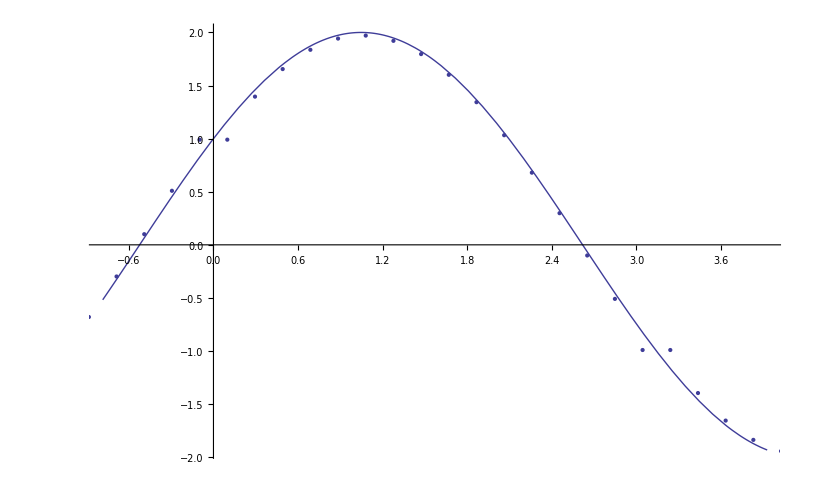

```mathematica
(* try dual-volume reg *)
dh=Table[(hetab[[tj+1]]-hetab[[tj]]),{tj,1,1+tjfc-tjs}];
sinhdh=Table[-(Cos[hetab[[tj+1]]]-Cos[hetab[[tj]]]),{tj,1,1+tjfc-tjs}];
modB1a=Table[(aphitab[[tj+1]]-aphitab[[tj]])/sinhdh[[tj]],{tj,1,1+tjfc-tjs}];
B1ab=Table[modB1a[[tj]]+B1b*dh[[tj]]/sinhdh[[tj]],{tj,1,1+tjfc-tjs}];
B1abnum=B1ab//.consts;
B1toplot=Table[{hctab[[tj]],B1abnum[[tj]]},{tj,1,1+tjfc-tjs}]//.consts;
p2B=ListPlot[B1toplot];
Show[{p1B,p2B}]
```

```mathematica
(* no help! *)
```